```mathematica
(* transform cartesian {x,y,z} to stereographic {X,Y} coordinates *)
cartesianToStereo[{x_,y_,z_}] := {x,y}/(1-z);
(* transform stereographic {X,Y} coordinates to cartesian {x,y,z} *)
stereoToCartesian[{x_,y_}] := {2x,2y,x^2+y^2-1}/(x^2+y^2+1);
(* transform spherical {θ,ϕ} to polar stereographic {r,ϕ} coordinates *)
sphericalToPolarStereo[{θ_,ϕ_}]:={Sin[θ]/(1-Cos[θ]), ϕ};
(* transform polar stereographic {r,ϕ} spherical {θ,ϕ} coordinates *)
polarStereoToSpherical[{r_,ϕ_}]:={2ArcTan[1/r], ϕ};

squareToHemisphereWithEqualArea[u1_,u2_]:=Module[
{sinLat,cosLat,longitude},
sinLat = u1;
cosLat=Sqrt[1-sinLat^2];
longitude=2π u2;
{Cos[longitude] cosLat, Sin[longitude] cosLat, sinLat}
];
```

```mathematica
spherePoints=Table[squareToHemisphereWithEqualArea[RandomReal[{-1,0}],RandomReal[{-1,0}]],{4*1024}];
Graphics3D[{
Opacity[0.5],{(*Blue,Point[spherePoints],*)Red,Point[#~Join~{0}&/@cartesianToStereo/@spherePoints]},
Opacity[0.2],Sphere[{0,0,0},1]
}]
```

-Graphics3D-

```mathematica
Manipulate[
Module[{shperePoint,stereoPoint},
shperePoint=squareToHemisphereWithEqualArea[u1,u2];
stereoPoint =cartesianToStereo[shperePoint]~Join~{0};
Graphics3D[
{
{
Blue,Point[shperePoint],Arrow[{{0,0,0},shperePoint}],
Red,Point[stereoPoint],Arrow[{{0,0,0},stereoPoint}],
},
Opacity[0.2],Sphere[{0,0,0},1]
},Axes->True,AxesLabel->{x,y,z}]],
{u1,-1,0},{u2,-1,0}]
```

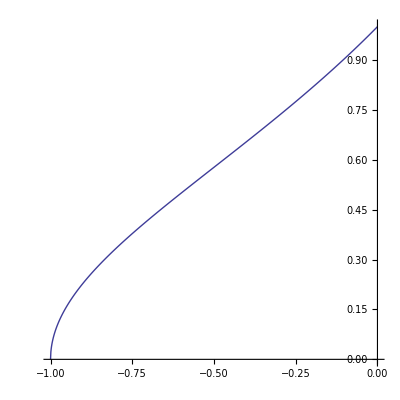

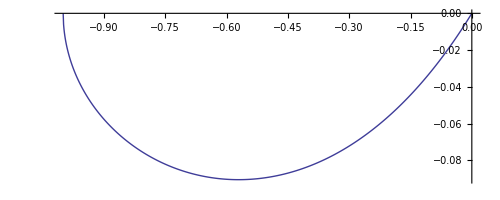

```mathematica
ListLinePlot[Table[{u1,cartesianToStereo[squareToHemisphereWithEqualArea[u1,0]][[1]] }, {u1,-1,0,0.001}],AspectRatio->1.0]
ListLinePlot[Table[{u1,cartesianToStereo[squareToHemisphereWithEqualArea[u1,0]][[1]] - (ArcSin[u1]/(Pi/2)+1)}, {u1,-1,0,0.001}],AspectRatio->Automatic]
```

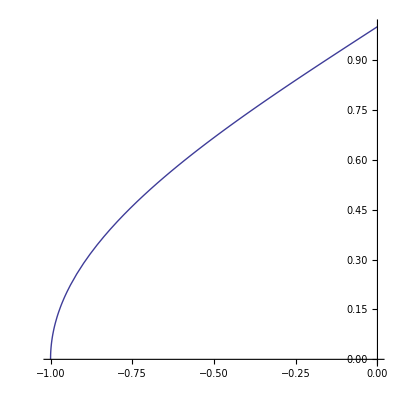

```mathematica
Plot[{ArcSin[x]/(Pi/2)+1},{x,-1,0},AspectRatio->1.0]
```